Homework 5
Homework Assignment 5: Design of a DNA neural network - Simulation and Annihilators

Simulation

### Define Reaction Functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* This Mathematica notebook is necessary. It can be download from the Simulation tab of the WTA Compiler website. *)
Get["CRNSimulator.wl"]
```

```mathematica
seesawAmp[x_,l_,r_List,rw_List]:=
Module[{f},
{seesaw[x,{l},{r,f}],
MapThread[conc[g[x,w[x,#1]],#2*c]&,{r,rw}],
conc[w[x,f],2*Apply[Plus,rw]*c]
}]/.List->Sequence
```

```mathematica
seesawInt[x_,l_List,r_,rw_]:={
seesaw[x,{l},{r}],
conc[g[x,w[x,r]],rw*c]
}/.List->Sequence
```

```mathematica
seesaw[x_,l_List,r_List]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#1,x]+g[x,w[x,#2]],g[w[#1,x],x]+w[x,#2],ks,ks]&,l,r],
(* Thresholding reactions *)
Outer[rxn[w[#,x]+th[w[#,x],x],waste,kf]&,l],
Outer[rxn[w[x,#]+th[x,w[x,#]],waste,kf]&,r],
(* Universal toehold binding reactions *)
Outer[revrxn[g[w[#,x],x]+W,g[w[#,x],x,W],kf,krf]&,l],
Outer[revrxn[g[x,w[x,#]]+W,g[W,x,w[x,#]],kf,krf]&,r],
Outer[revrxn[th[w[#,x],x]+W,th[W,w[#,x],x],kf,krs]&,l],
Outer[revrxn[th[x,w[x,#]]+W,th[x,w[x,#],W],kf,krs]&,r],
Outer[revrxn[w[#,x]+G,w[#,x,G],kf,krf]&,l],
Outer[revrxn[w[x,#]+G,w[x,#,G],kf,krf]&,r],
Outer[revrxn[w[#,x]+TH,w[#,x,TH],kf,krs]&,l],
Outer[revrxn[w[x,#]+TH,w[x,#,TH],kf,krs]&,r],
(* Leak reactions *)
Outer[rxn[g[w[#1,x],x]+w[#2,x],g[w[#2,x],x]+w[#1,x],kl]&,l,l],
Outer[rxn[g[x,w[x,#1]]+w[x,#2],g[x,w[x,#2]]+w[x,#1],kl]&,r,r]
}/.List->Sequence
```

```mathematica
reporter[x_,l_,conx_:2]:={
(* Toehold exchange reactions *)
rxn[w[l,x]+Rep[x],Fluor[x],2*ks],
(* Universal toehold binding reactions *)
revrxn[Rep[x]+W, Rep[x,W],kf,krf],
revrxn[w[l,x]+G,w[l,x,G],kf,krf],
revrxn[w[l,x]+TH,w[l,x,TH],kf,krs],
(* Complex Concentrations *)
conc[Rep[x],conx*c]
}/.List->Sequence
```

```mathematica
annihilator[l_List,x_,r_List,y_,conx_:4]:={
(* Toehold exchange reactions *)
Outer[revrxn[w[#,x]+A[x,y],A[w[#,x],y],kf,kr]&,l],
Outer[revrxn[w[#,y]+A[x,y],A[w[#,y],x],kf,kr]&,r],
Outer[rxn[w[#1,y]+A[w[#2,x],y],waste,kf]&,r,l],
Outer[rxn[w[#1,x]+A[w[#2,y],x],waste,kf]&,l,r],
(* Universal toehold binding reactions *)
revrxn[W+A[x,y],A[W,x,y],kf,krs],
revrxn[W+A[x,y],A[x,y,W],kf,krs],
revrxn[W+A[x,y,W],A[W,x,y,W],kf,krs],
revrxn[W+A[W,x,y],A[W,x,y,W],kf,krs],
Outer[revrxn[W+A[w[#,x],y],A[w[#,x],y,W],kf,krs]&,l],
Outer[revrxn[W+A[w[#,y],x],A[w[#,y],x,W],kf,krs]&,r],
(* Toehold exchange on spurious products *)
Outer[revrxn[w[#,x]+A[x,y,W],A[w[#,x],y,W],kf,kr]&,l],
Outer[revrxn[w[#,y]+A[W,x,y],A[w[#,y],x,W],kf,kr]&,r],
(* Complex Concentrations *)
conc[A[x,y],conx*c]
}/.List->Sequence
```

```mathematica
WTA[x_List,l_List,conx_:1.5] :={
(* Define annihilator reaction for each pair of domains *)
Table[annihilator[{l[[i]]},x[[i]],{l[[j]]},x[[j]],conx],{i,1,Length[x]-1},{j,i+1,Length[x]}]
}/.List->Sequence
```

```mathematica
memColors={
ColorData["FallColors"][0],
ColorData["FallColors"][1],
ColorData["FallColors"][0.5],
RGBColor[70/255,130/255,180/255], 
RGBColor[98/255,82/255,122/255],
RGBColor[242/255,174/255,114/255],
 RGBColor[217/255,100/255,89/255],
RGBColor[236/255,161/255,166/255]};
```

```mathematica
memColorRules={-1->Lighter[Gray,0.4],0->Lighter[Gray,0.8],1->ColorData["FallColors"][0]}
```

{-1→RGBColor[0.7, 0.7, 0.7],0→RGBColor[0.9, 0.9, 0.9],1→RGBColor[0.259739, 0.395895, 0.39585]}

```mathematica
testColorRules={-1->Lighter[Gray,0.4],0->Lighter[Gray,0.8],1->ColorData["FallColors"][1]}
```

{-1→RGBColor[0.7, 0.7, 0.7],0→RGBColor[0.9, 0.9, 0.9],1→RGBColor[0.961303, 0.793622, 0.261418]}

### Load WTA Compiler Input File

Make sure you run the above “Define Reaction Functions” section. If there is an error, double check that you downloaded the “CRNSimulator.wl” file from the WTA Compiler website.

This notebook assumes itself, CRNSimulator.wl, and your user-modified-WTA.csv files are all in the same folder.

```mathematica
(* enter the name of the file containing memories and inputs *)
fileName="wtaData.csv";
```

```mathematica
inputfile=Import[fileName];
header=inputfile[[1]];
data=Transpose[inputfile[[2;;]]];
```

```mathematica
memory={};
test={};

For[i=1,i<=Length[header],i++,
If[StringTake[header[[i]],6]=="memory",AppendTo[memory,data[[i]]]];
If[StringTake[header[[i]],4]=="test",AppendTo[test,data[[i]]]];
];
```

```mathematica
CanvasRow=Ceiling[Sqrt[Length[memory[[1]]]]];
CanvasColumn=Floor[Sqrt[Length[memory[[1]]]]];
```

```mathematica
colorFunction[value_]:=Module[{},
If[value<0,Lighter[Gray,0.4],
If[value≥0,Blend[{{0,Lighter[Gray,0.8]},{Max[memory],ColorData["FallColors"][0]}},value]]]
]
```

```mathematica
Grid[{Table[ArrayPlot[Partition[memory[[i]],CanvasColumn],Mesh->True,MeshStyle->Directive[{White,Thick}],ColorFunction->(colorFunction[#]&),ColorFunctionScaling->False, ImageSize->125,
PlotRange->{0,Max[memory]},PlotLabel->Style[header[[i]],Black,FontFamily->"Helvetica",FontSize->20]],{i,1,Length[memory]}]}]
```

-Graphics- | -Graphics-

```mathematica
Grid[{Table[
ArrayPlot[Partition[test[[i]],CanvasColumn],Mesh->True,MeshStyle->Directive[{White,Thick}],ColorRules->testColorRules, ImageSize->125,PlotLabel->Style["test["<>ToString[i]<>"]",Black,FontFamily->"Helvetica",FontSize->20]],{i,1,Length[test]}]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(* Normalize each memory to sum to 1x *)
memoryNorm=Map[#/Total[Cases[#,n_/;n>0]]&,memory];
```

### Plot the Weighted-Sum Space

```mathematica
nMems = Length[memory];
xydata=(test/.-1->0).Transpose@memoryNorm;
plotColors=Directive[{Opacity[1],AbsolutePointSize[12],memColors[[First[Ordering[#,-1]]]]}]&/@xydata;
```

```mathematica
testImages=Table[
ArrayPlot[Partition[test[[i]],CanvasColumn],Mesh->True,MeshStyle->Directive[{White,Thin}],ColorRules->testColorRules, ImageSize->42,PlotLabel->Style["test["<>ToString[i]<>"]",Black,FontFamily->"Helvetica",FontSize->11],ImageMargins->8],{i,1,Length[test]}];
```

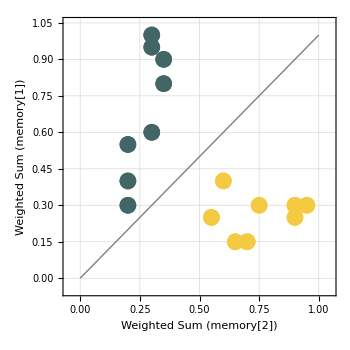

```mathematica
Grid[{Table[
ListPlot[List/@MapThread[Tooltip[Reverse@#1,#2,TooltipStyle->{Background->White}]&,{xydata[[All,set]],testImages}],
PlotStyle->plotColors,
PlotRange->{{-0.05,1.05},{-0.05,1.05}},ImageSize->350,AspectRatio->1,
Frame->True,GridLines->Automatic,LabelStyle->Directive[FontSize->18,Black,FontFamily->"Helvetica"],
FrameLabel->{Style["Weighted Sum ("<>ToString[header[[set[[2]]]]]<>")",Black,FontSize->18,FontFamily->"Helvetica"],
Style["Weighted Sum ("<>ToString[header[[set[[1]]]]]<>")",Black,FontSize->18,FontFamily->"Helvetica"]},

Prolog->{Thick,Gray,Line[{{0,0},{1,1}}]}],{set,Subsets[Range[nMems],{2}]}]}]
```

### Simulate DNA-based Winner Take All Network

#### Define Reaction Parameters

```mathematica
rates={
kr -> 4,(* 0.4, slow strand dissociation rate on matching annihilator, unit: /s *)
kf -> 2*10^6, (* 2*10^6, fast strand displacement rate with extended toehold, unit: /M/s *)
ks -> 5*10^4, (* 5*10^4, slow strand displacement rate with universal toehold, unit: /M/s *)
krf -> 26, (* 26, fast strand dissociation rate with universal toehold, unit: /s *)
krs -> 1.3, (* 1.3, slow strand dissociation rate with extended toehold, unit: /s *)
kl -> 10 (* 10, strand displacement leak rate, unit: /M/s *) 
};
```

```mathematica
time=8; (* simulation time, unit: hours *)
c = 100*10^-9; (* standard concentration, unit: M (Molar) *)
anhConc=4; (* annihilator concentration relative to the standard concentration *)
```

#### Run Simulation and Plot Kinetics

```mathematica
(* Simulate *)
SIMcircuit=Table[
nBits=Length[Position[test[[1]],1]];
rsys=Flatten@{
(* Creates list of input seesaw gates for multiplying inputs *)
Table[seesawAmp["x"<>ToString[n],h,Range[nMems],memoryNorm[[;;,n]]],{n,Flatten@Position[xs,1]}],

(* Creates the seesaw integration gates for computing the weighted sum *)
Table[
seesawInt[i,Table["x"<>ToString[n],{n,Flatten@Position[xs,1]}],i+nMems,1],
{i,nMems}],

(* Creates the seesaw gates and annihilators for WTA computation *)
WTA[Range[nMems+1,nMems*2],Range[nMems],anhConc],

(* Creates the seesaw amplification gates for restoring the winning signal *)
Table[
seesawAmp[i+nMems,i,{i+2*nMems},{1}],
{i,nMems}],

(* Creates the seesaw reporters *)
Table[
reporter[i+2*nMems,{i+nMems}],
{i,nMems}],

(* Defines input strands for each test case *)
Table[conc[w[h,"x"<>ToString[n]],1/nBits*c],{n,Flatten@Position[xs,1]}],

(* Creates reactions to simulate binding to shared toehold sequences *)
conc[W,(2*Total[Select[Flatten[memoryNorm],#>0&]]+Total[xs]/nBits+2*nMems)*c],
conc[G,(Total[Select[Flatten[memoryNorm],#>0&]]+nMems*(1+1+2))*c],
conc[TH,(2*Binomial[nMems,2]-nMems+1)*c]
}/.rates;

sol=SimulateRxnsys[rsys,time*60*60]//ReleaseHold//Flatten;

(* Return the simulated concentration for these species *)
 Table[Fluor[i+2*nMems][t*60*60]/c/.sol,{i,nMems}],

(* Loop over these test cases *)
{xs,test}];
```

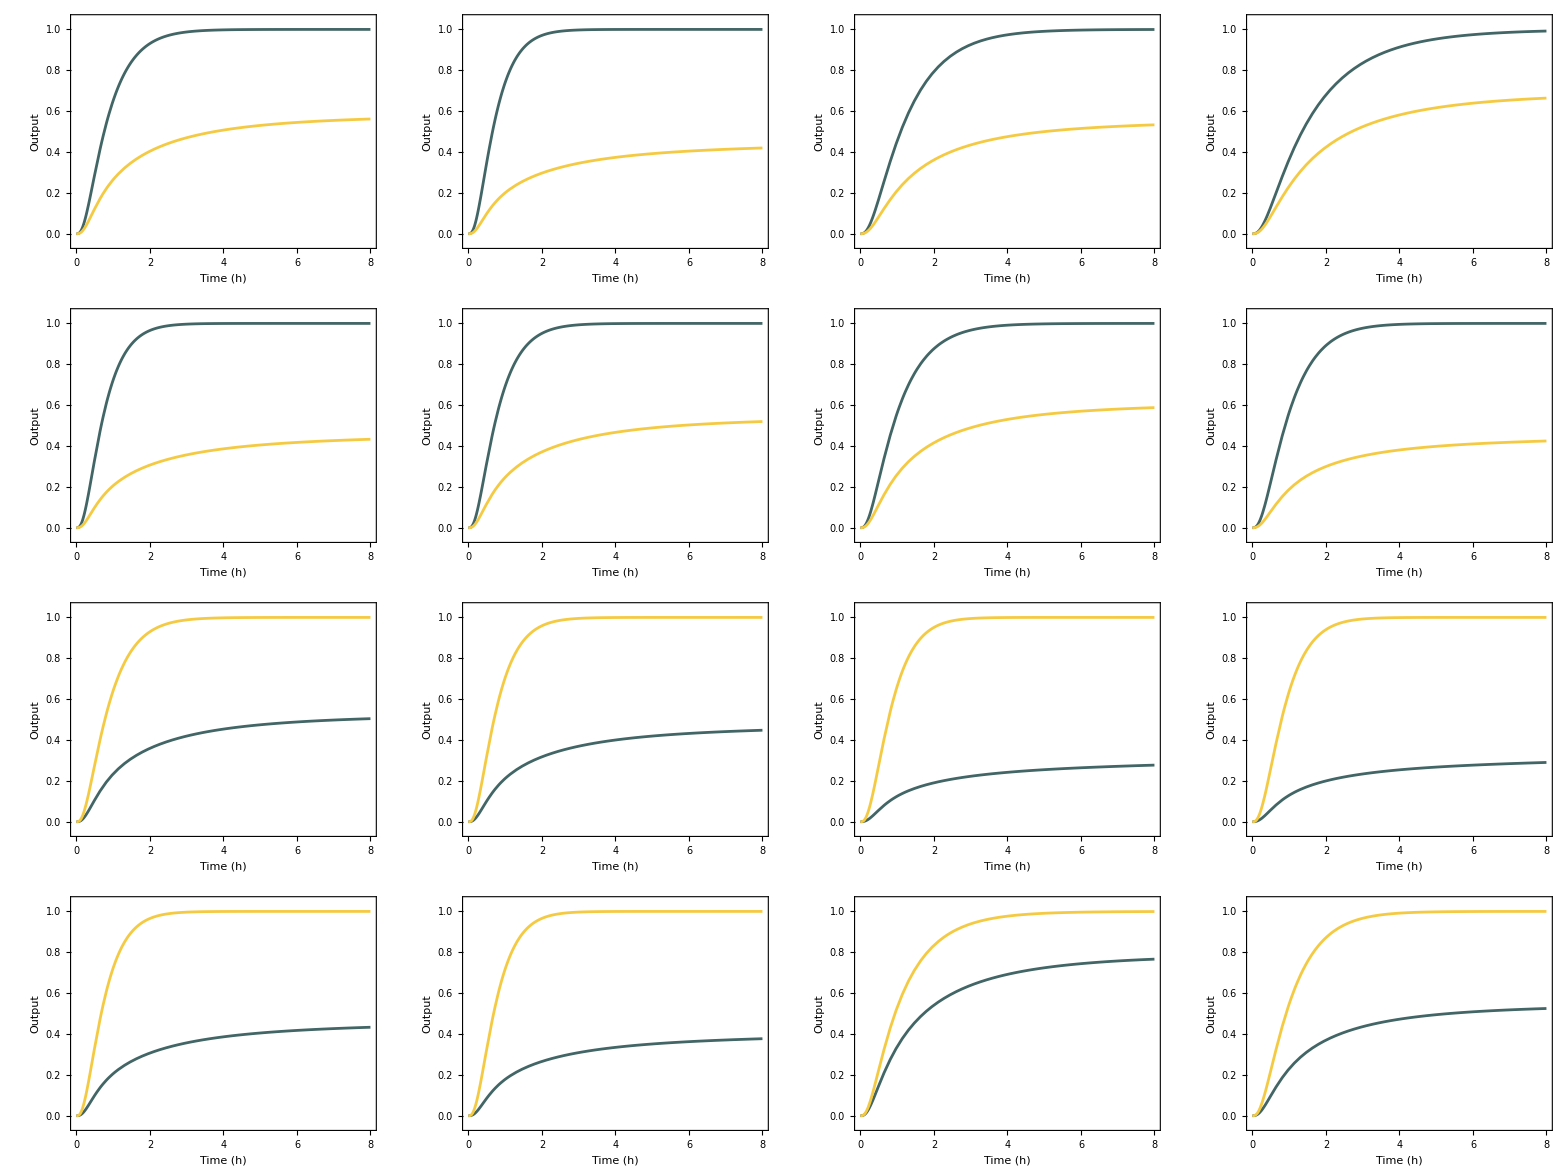

```mathematica
(*Make 1 plot for each test*)
Legended[Grid[ArrayReshape[Table[
Plot[SIMcircuit[[w]],{t,0,time},Evaluated->True,PlotStyle->Table[{AbsoluteThickness[2],ColorData["FallColors"][c]},{c,{0,1,0.5}}],
ImageSize->220,Frame->True,AspectRatio->1/1.3,PlotRange->{{Automatic,time},{-0.05,1.05}},
LabelStyle->Directive[FontSize->18,FontFamily->"Helvetica"],
Prolog->Inset[ArrayPlot[Partition[test[[w]],CanvasColumn],Mesh->True,MeshStyle->White,ColorRules->testColorRules/.(1->Black),Frame->False,ImageSize->45],Scaled[{.20,.75}]],
FrameLabel->{Style["Time (h)",FontSize->16,FontFamily->"Helvetica"],Style["Output",FontSize->16,FontFamily->"Helvetica"]}],
{w,Length[test]}],{Ceiling[Length[test]/4],4},""]],
Pane[LineLegend[Table[Directive[AbsoluteThickness[4],ColorData["FallColors"][c]],{c,{0,1,0.5}}],Map[ArrayPlot[Partition[#,CanvasColumn],Mesh->True,MeshStyle->White,ColorRules->memColorRules/.(1->Black),ImageSize->60]&,memory],LabelStyle->Directive[FontSize->16,FontFamily->"Helvetica"],LegendMarkerSize->35,LegendLabel->"Memories"],ImageMargins->{{25,0},{0,0}}]]
```

The output trajectories are fairly similar across the test patterns and all are classified correctly. There are differences in trajectories of the different patterns, with patterns that less similar to the memories having a slower “correct memory” trajectories and a slightly higher “incorrect memory” trajectory. We would expect this as these memories are harder to classify so will have a closer concentration before the annihilation step.

Annihilators

The kf rate represents the binding reaction of the extended toehold, so it will be around 2*10^6.
The kr represents the unbinding reaction of the extended toehold so is around 10^(6-L), where L is the length of the extended toehold. Since the toehold is 5 nucleotides long and the  extended toehold domain on the annihilator is 2 nucleotides long, so L = 7 and kr = 10^-1 = 0.1.

Increasing the annihilator concentration will lower the trajectories, but will still give the correct output. This is because all the molecules will be bound by annihilators at a fast rate and will have a higher likelihood of binding to an annihilator will more of them present, so will not be able to go through the signal amplification as fast as with a lower annihilator concentration even for the higher concentration species. This is supported in the simulation and can be seen by changing the annihilator concentration to a higher number, such as 100:

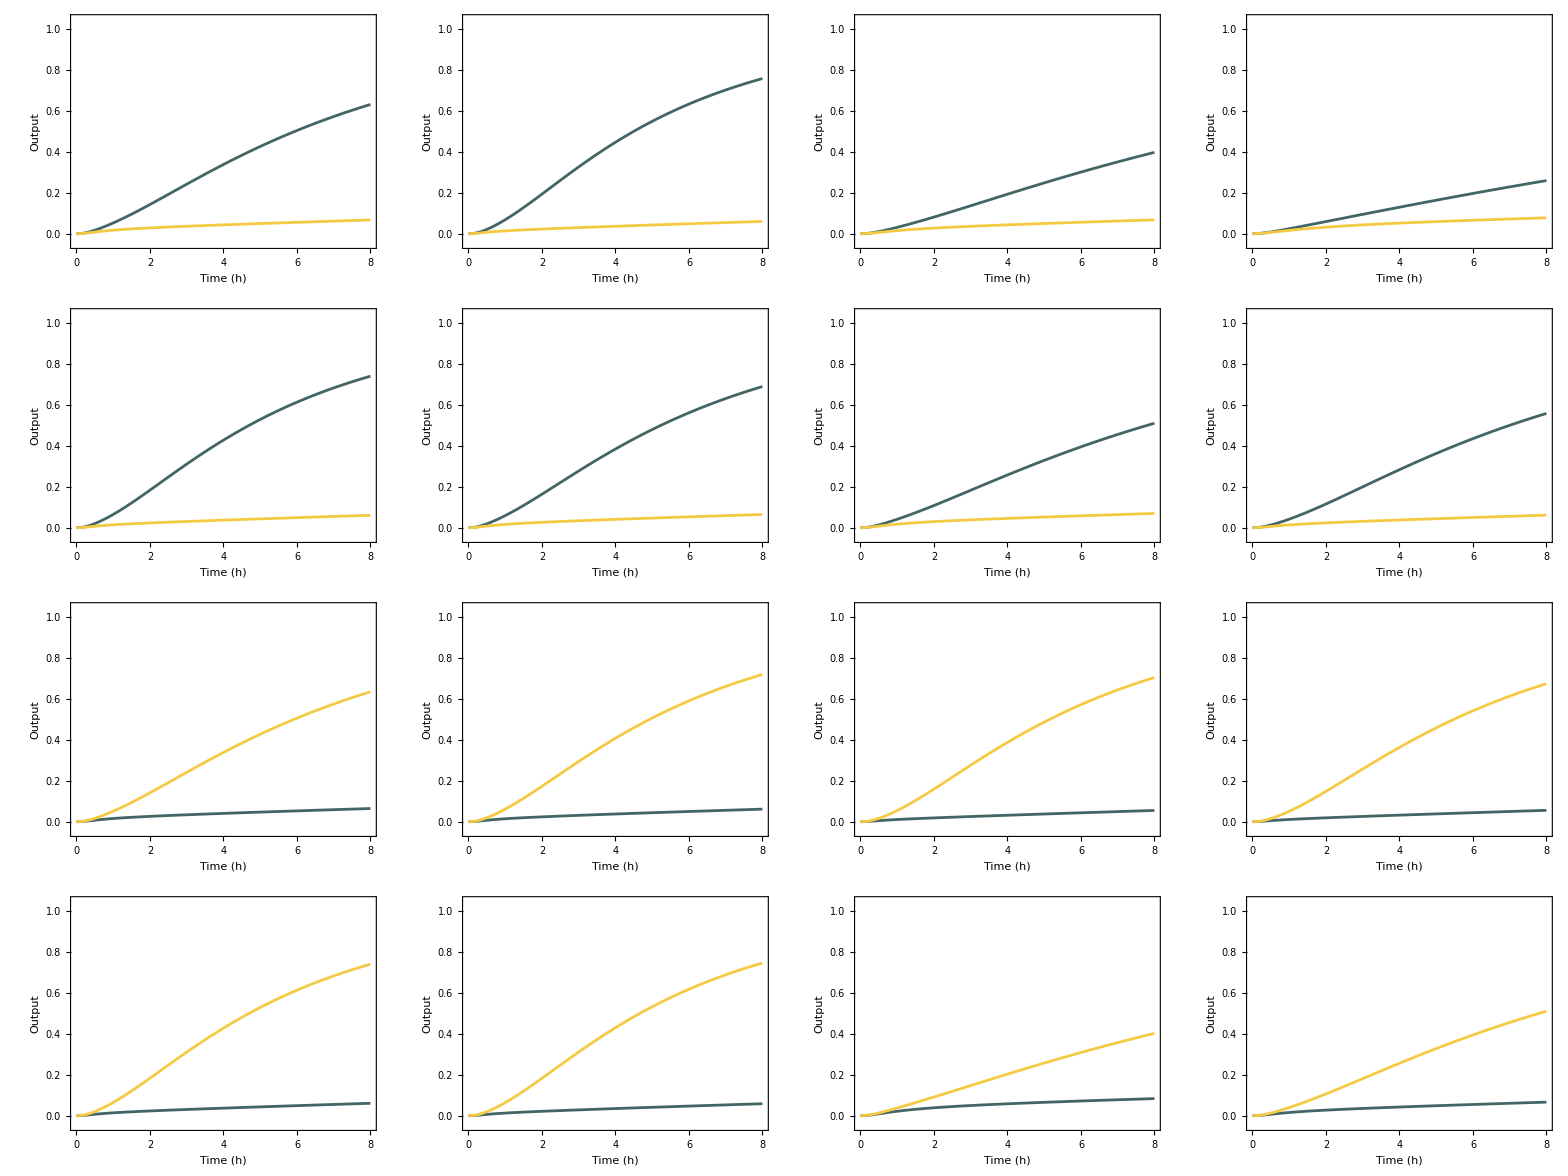

Decreasing the annihilator concentration will raise the trajectories and can give an incorrect output. This is because there will be fewer annihilator molecules to bind the species , so molecules will go through the signal amplification step before they can annihilated quick enough. If the concentration is low enough then both outputs will go to 1. This is supported in the simulation and can be seen by changing the annihilator to a lower number, such as  1 or 0.01:

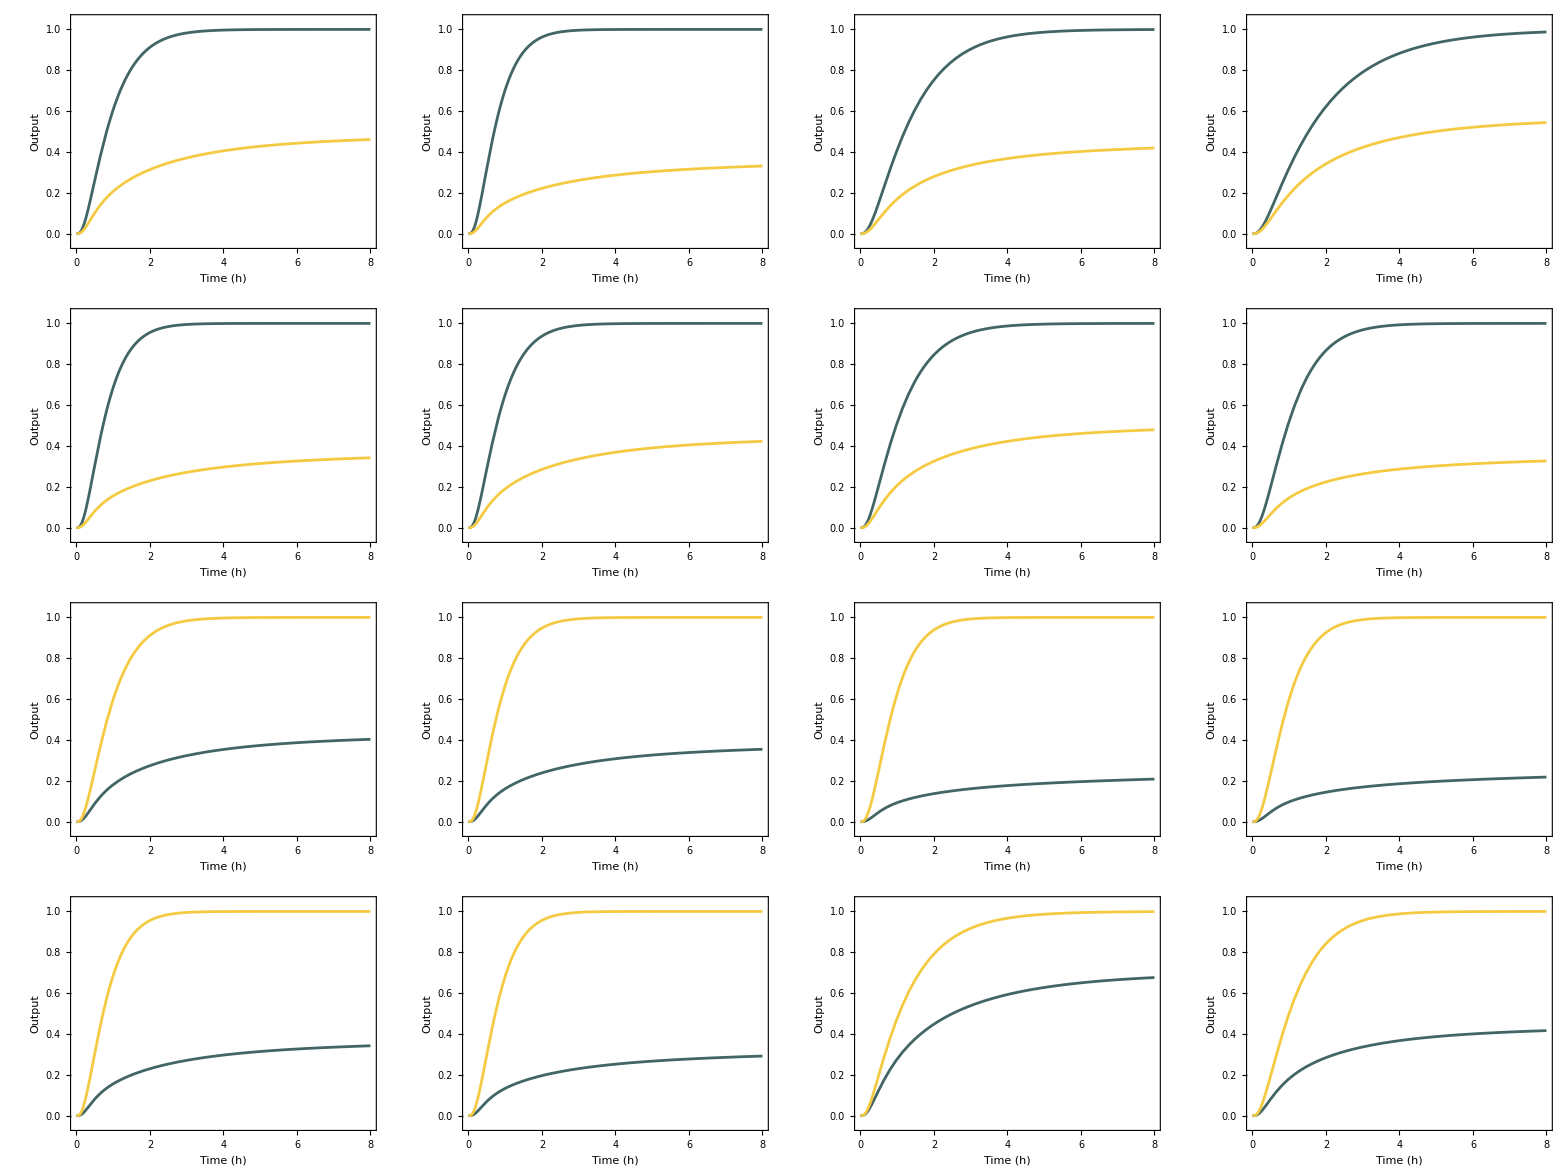

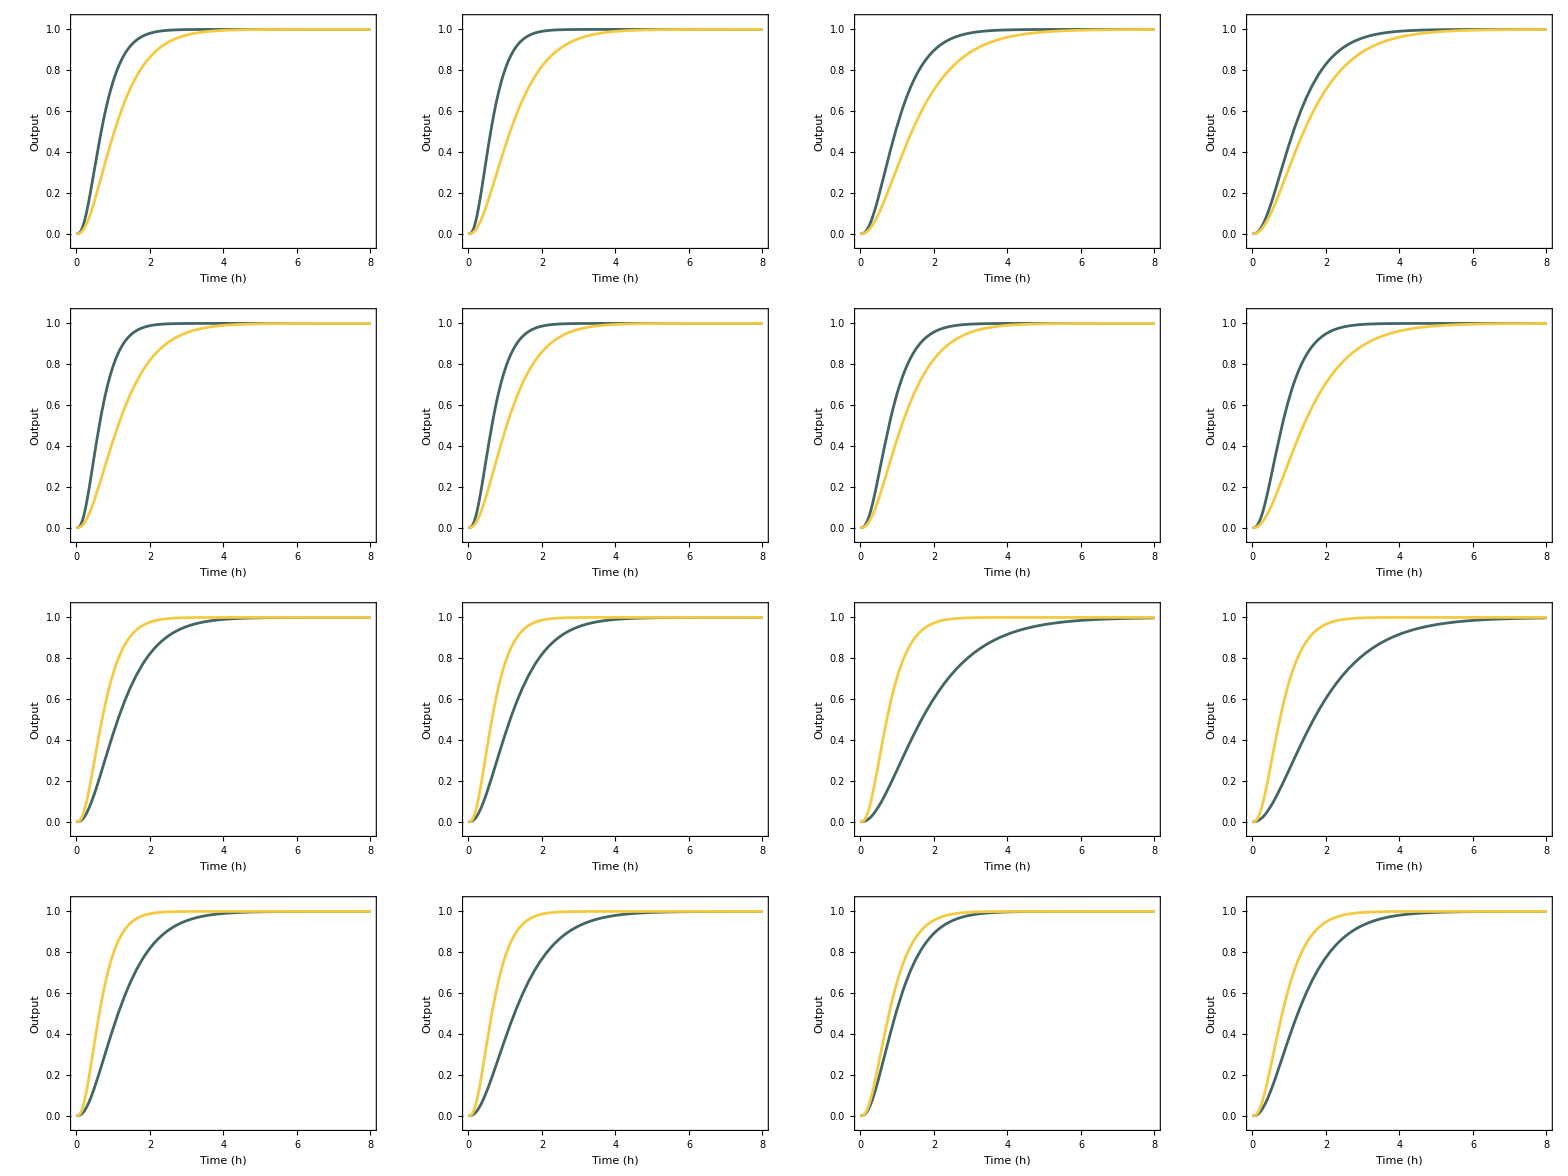

Changing the length of the extended toehold domains will only change kr.  Increasing the length will decrease kr and decreasing the length will increase kr. 
Decreasing kr will lower the trajectories, but will still give the correct output. This is because the molecules be released from the annihilator at a slower rate, so will not be able to go through the signal amplification as fast even for the higher concentration species. This is supported in the simulation and can be seen by changing kr to a lower number, such as 0.04:

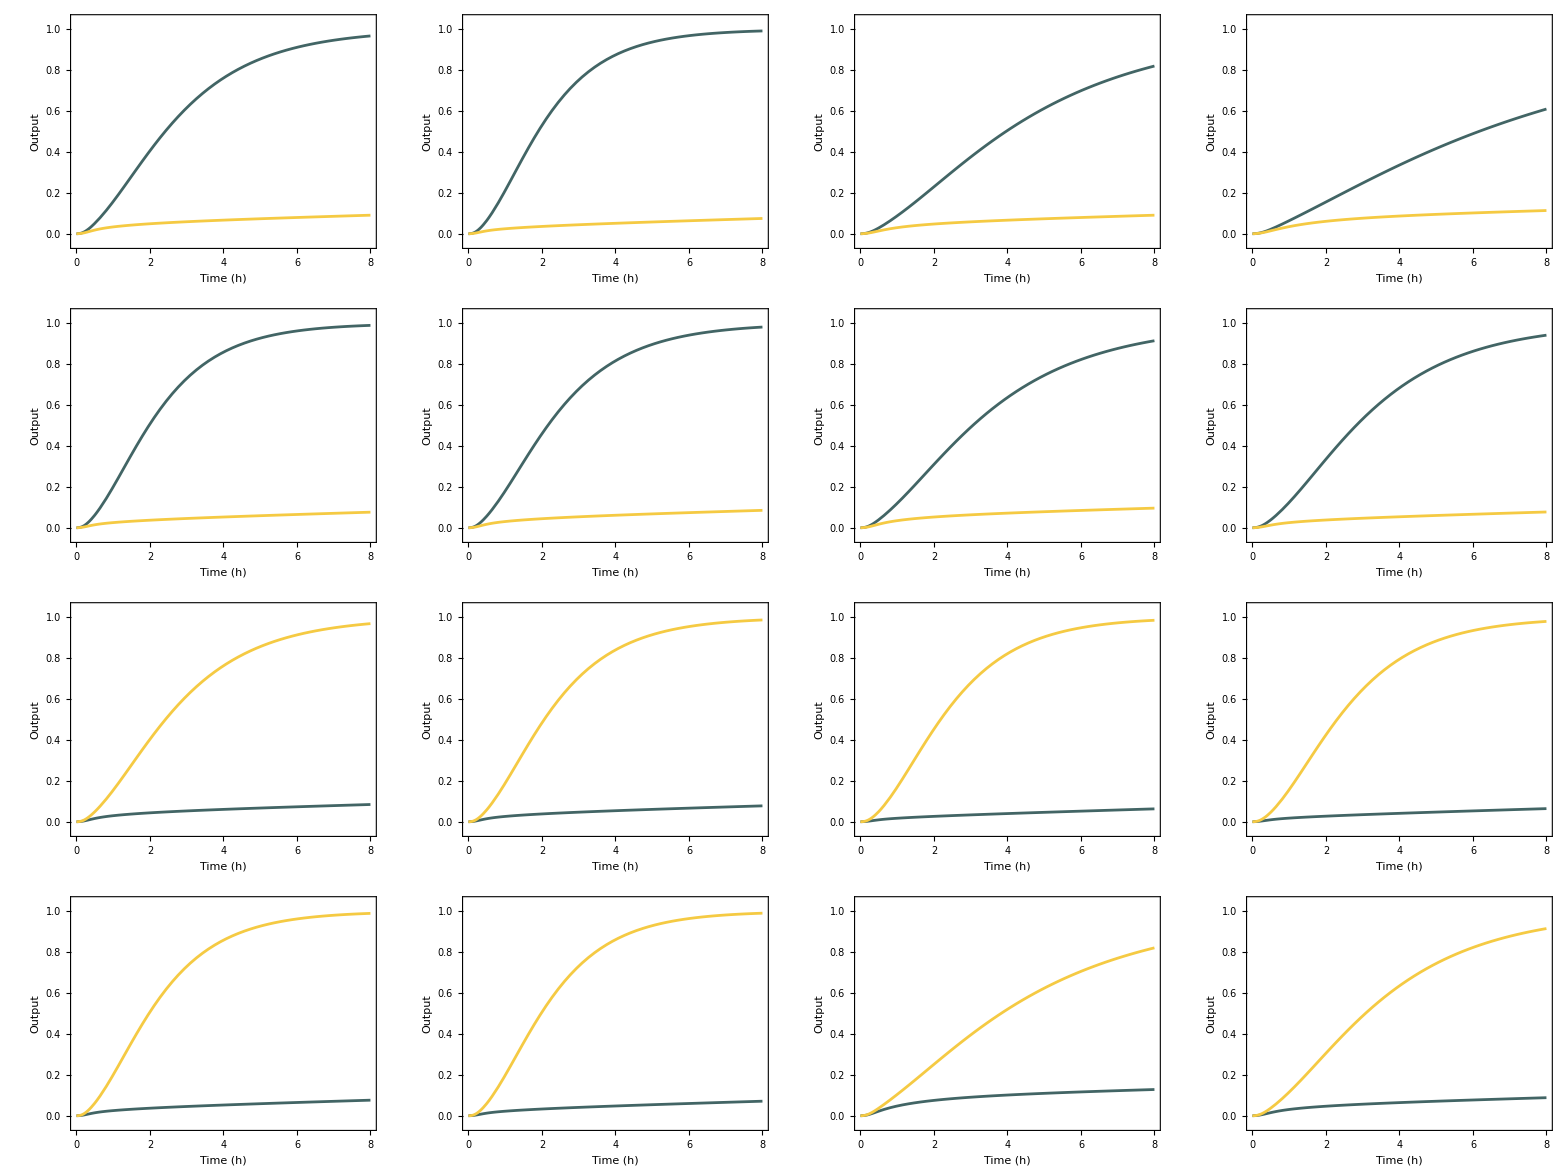

Increasing kr will raise the trajectories and can possibly give an incorrect output. This is because the molecules will be released from the annihilator at a faster rate, so the annihilators will have a lower chance of binding both species and will allow more of each species to get  amplified. This is supported in the simulation and can be seen by changing kr to a higher number, such as 4:

-Graphics-